# Motor Characterization Analysis

```mathematica
SetDirectory@NotebookDirectory[];
```

## Load and parse the data

```mathematica
SetDirectory@NotebookDirectory[];
```

```mathematica
Import["test results 12-12-2016.txt","Elements"]
```

{Data,Lines,Plaintext,String,Words}

```mathematica
data=Import["test results 12-12-2016.txt","Lines"];
data=Cases[data,Except[""]][[2;;]];
data=Split[data,And[StringContainsQ[#1,"Current"],StringContainsQ[#2,"Current"]]&];
weights=StringSplit[#,"g"][[1]]&/@Flatten@data[[1;;;;2]];
data=data[[2;;;;2]];
parsed=Flatten@MapThread[Map[(result@@Prepend[ToExpression/@(StringSplit[#,","][[2;;;;2]]),weight]&)/.weight->ToExpression@#1,#2]&,{weights,data}];
```

```mathematica
"result[mass,power,current,speed]"
Column@parsed;
```

result[mass,power,current,speed]

### Convert the data to standard units

```mathematica
final=parsed;
final[[All,1]]=N@UnitConvert[(final[[All,1]]*Quantity[, "Grams"]+Quantity[5, "Grams"])*Quantity[, "StandardAccelerationOfGravity"]*Quantity[2.5, "Centimeters"],"Newton-Meters"];
final[[All,2]]=N@final[[All,2]]/255;
final[[All,3]]=final[[All,3]]*Quantity[5, "Volts"]/1023;
final[[All,4]]=final[[All,4]]/12*Quantity[, ("Revolutions")/("Seconds")];
```

```mathematica
"result[mass,power,current,speed]"
Column@final;
```

result[mass,power,current,speed]

## Plot and analyze the data

```mathematica
weightGroupings=SortBy[#,(#[[2]]&)]&/@GroupBy[final,#[[1]]&];
Column@weightGroupings;
```

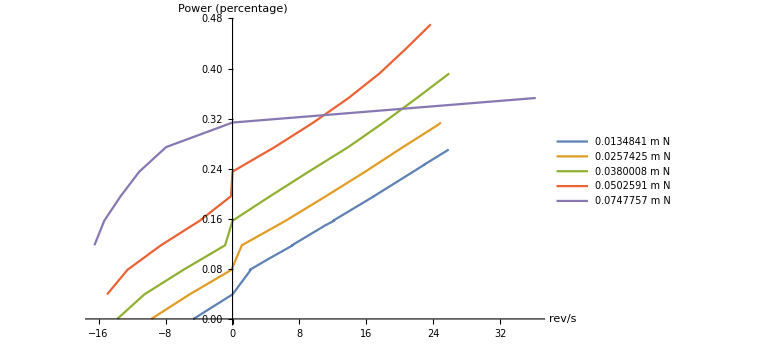

```mathematica
ListLinePlot[({#[[4]],#[[2]]}&/@#)&/@Values@weightGroupings,AxesLabel->{Automatic,"Power (percentage)"},PlotLegends->Keys@weightGroupings,ImageSize->Large]
```

## Guess the form of the key equation

```mathematica
ClearAll[power]
power[torque_,speed_]:=Module[{sol,deadzonespeed,deadzoneadjust},
sol=k1 (torque+k5) -k2 speed;
deadzonespeed=Max[Min[k3,speed],-k3];
deadzoneadjust=k4 deadzonespeed;
sol+deadzoneadjust
]
```

## Fit the data

```mathematica
tspdata=QuantityMagnitude[List@@@final[[;;-2,{1,4,2}]]];
```

```mathematica
fit=FindFit[tspdata,power[t,s],{k1,k2,k3,k4,k5},{t,s}]
```

{k1→4.72363,k2→-0.00890588,k3→0.194554,k4→0.0695813,k5→-0.00611036}

```mathematica
fitted=Table[power[torque,speed],{torque,QuantityMagnitude@Keys@weightGroupings}]/.fit
```

{0.034831+0.00890588 speed+0.0695813 Max[-0.194554,Min[0.194554,speed]],0.0927347+0.00890588 speed+0.0695813 Max[-0.194554,Min[0.194554,speed]],0.150638+0.00890588 speed+0.0695813 Max[-0.194554,Min[0.194554,speed]],0.208542+0.00890588 speed+0.0695813 Max[-0.194554,Min[0.194554,speed]],0.324349+0.00890588 speed+0.0695813 Max[-0.194554,Min[0.194554,speed]]}

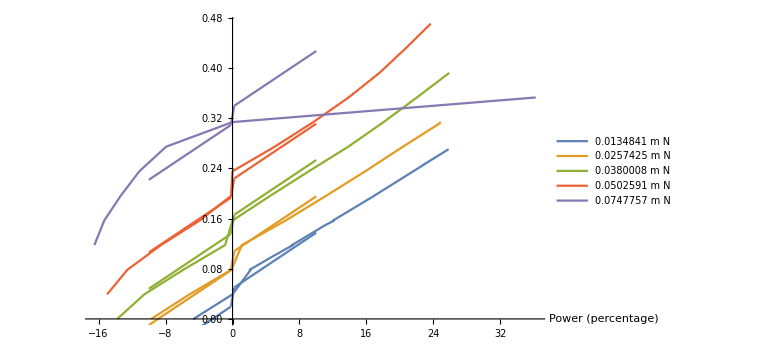

```mathematica
fitplot=Plot[fitted,{speed,-10,10}];
dataplot=ListLinePlot[({#[[4]],#[[2]]}&/@#)&/@Values@weightGroupings,AxesLabel->{"Power (percentage)",Automatic},PlotLegends->Keys@weightGroupings,ImageSize->Large];
Show[dataplot,fitplot]
```

```mathematica
CForm[ power[torque,speed]/.fit]
```

0.008905883532020176*speed + 4.723625131842297*(-0.006110361807961874 + torque) + 
   0.06958126214652462*Max(-0.19455445221646883,Min(0.19455445221646883,speed))